# Medfly Data Analysis

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
GetDataset[experimentsIDs_,dataCorrected_]:=dataCorrected[[#]]&/@experimentsIDs
GetDatasetQuartiles[experimentsIDs_,dataCorrected_]:=Module[{experimentData,lowQuartile,midQuartile,highQuartile},
experimentData=GetDataset[experimentsIDs,dataCorrected];
lowQuartile=((Quantile[#,.25]&/@(experimentData//Transpose))//N);
midQuartile=((Quantile[#,.5]&/@(experimentData//Transpose))//N);
highQuartile=((Quantile[#,.75]&/@(experimentData//Transpose))//N);
{lowQuartile,midQuartile,highQuartile}
]
```

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9

## PopDynamics

```mathematica
{experimentID,folderID}={5,1};
folderList={
"./Datasets/Fertile_WDXX/Visual/",
"./Datasets/Infertile_WDXX/OneReleaseSixValues/",
"./Datasets/Infertile_WDXX/FiveReleaseSixValues/"
};
folder=folderList[[folderID]];
```

Males

```mathematica
fileNames=FileNames[folder<>"ADM*.csv"];
```

```mathematica
(*Setup directory and load filenames*)
fileNames=FileNames[folder<>"ADM*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[Import[#][[All,2;;All]]&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Define labels and swatches*)
horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}]
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
dataCorrectedM=dataCorrected;
Transpose[{Range[labels//Length],labels}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}}

{{DD_XY,RGBColor[0.293416, 0.0574044, 0.529412]},{WD_XY,RGBColor[0.3361115263157895, 0.13164028421052631, 0.5894257368421052]},{DR_XY,RGBColor[0.378807052631579, 0.2058761684210526, 0.6494394736842105]},{DB_XY,RGBColor[0.4215025789473684, 0.2801120526315789, 0.7094532105263158]},{WW_XY,RGBColor[0.4641981052631579, 0.35434793684210525, 0.769466947368421]},{RW_XY,RGBColor[0.5068936315789474, 0.42858382105263154, 0.8294806842105262]},{BW_XY,RGBColor[0.5495891578947368, 0.5028197052631578, 0.8894944210526315]},{RR_XY,RGBColor[0.5847483684210526, 0.5611895263157894, 0.9099760526315789]},{BR_XY,RGBColor[0.6161394210526315, 0.6116263157894737, 0.9106916315789474]},{BB_XY,RGBColor[0.6475304736842105, 0.6620631052631578, 0.9114072105263158]},{DD_XX,RGBColor[0.6789215263157895, 0.712499894736842, 0.9121227894736842]},{WD_XX,RGBColor[0.7103125789473683, 0.7629366842105263, 0.9128383684210526]},{DR_XX,RGBColor[0.7417036315789474, 0.8133734736842105, 0.9135539473684211]},{DB_XX,RGBColor[0.7720281052631578, 0.8501316842105263, 0.909821105263158]},{WW_XX,RGBColor[0.8002194210526316, 0.8595327368421053, 0.8971914210526316]},{RW_XX,RGBColor[0.8284107368421052, 0.8689337894736842, 0.8845617368421053]},{BW_XX,RGBColor[0.856602052631579, 0.8783348421052631, 0.8719320526315789]},{RR_XX,RGBColor[0.8847933684210526, 0.8877358947368421, 0.8593023684210527]},{BR_XX,RGBColor[0.9129846842105263, 0.897136947368421, 0.8466726842105263]},{BB_XX,RGBColor[0.941176, 0.906538, 0.834043]},{Total,RGBColor[0.25, 0.25, 0.25]}}

{{1,DD_XY},{2,WD_XY},{3,DR_XY},{4,DB_XY},{5,WW_XY},{6,RW_XY},{7,BW_XY},{8,RR_XY},{9,BR_XY},{10,BB_XY},{11,DD_XX},{12,WD_XX},{13,DR_XX},{14,DB_XX},{15,WW_XX},{16,RW_XX},{17,BW_XX},{18,RR_XX},{19,BR_XX},{20,BB_XX},{21,Total}}

```mathematica
{lowQuartile,midQuartile,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrected];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0025],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
males=Show[b,a,c,
PlotRange->All,
Frame->True,
BaseStyle->15,
GridLines->Automatic,
FrameStyle->Thickness[.005],
ImageSize->800,
AspectRatio->1
];
```

Females

```mathematica
experimentIDindicesA={"0.013"};
experimentIDindicesB={"0.006"};
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
fileNames=FileNames[folder<>"AF1_Aggregate*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[Import[#][[All,2;;All]]&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Define labels and swatches*)
horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}]
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
dataCorrectedF=dataCorrected;
(**)
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}}

{{DD_XY,RGBColor[0.293416, 0.0574044, 0.529412]},{WD_XY,RGBColor[0.3361115263157895, 0.13164028421052631, 0.5894257368421052]},{DR_XY,RGBColor[0.378807052631579, 0.2058761684210526, 0.6494394736842105]},{DB_XY,RGBColor[0.4215025789473684, 0.2801120526315789, 0.7094532105263158]},{WW_XY,RGBColor[0.4641981052631579, 0.35434793684210525, 0.769466947368421]},{RW_XY,RGBColor[0.5068936315789474, 0.42858382105263154, 0.8294806842105262]},{BW_XY,RGBColor[0.5495891578947368, 0.5028197052631578, 0.8894944210526315]},{RR_XY,RGBColor[0.5847483684210526, 0.5611895263157894, 0.9099760526315789]},{BR_XY,RGBColor[0.6161394210526315, 0.6116263157894737, 0.9106916315789474]},{BB_XY,RGBColor[0.6475304736842105, 0.6620631052631578, 0.9114072105263158]},{DD_XX,RGBColor[0.6789215263157895, 0.712499894736842, 0.9121227894736842]},{WD_XX,RGBColor[0.7103125789473683, 0.7629366842105263, 0.9128383684210526]},{DR_XX,RGBColor[0.7417036315789474, 0.8133734736842105, 0.9135539473684211]},{DB_XX,RGBColor[0.7720281052631578, 0.8501316842105263, 0.909821105263158]},{WW_XX,RGBColor[0.8002194210526316, 0.8595327368421053, 0.8971914210526316]},{RW_XX,RGBColor[0.8284107368421052, 0.8689337894736842, 0.8845617368421053]},{BW_XX,RGBColor[0.856602052631579, 0.8783348421052631, 0.8719320526315789]},{RR_XX,RGBColor[0.8847933684210526, 0.8877358947368421, 0.8593023684210527]},{BR_XX,RGBColor[0.9129846842105263, 0.897136947368421, 0.8466726842105263]},{BB_XX,RGBColor[0.941176, 0.906538, 0.834043]},{Total,RGBColor[0.25, 0.25, 0.25]}}

```mathematica
{lowQuartile,midQuartile,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrected];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0025],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
females=Show[b,a,c,
PlotRange->All,
Frame->True,
BaseStyle->15,
GridLines->Automatic,
FrameStyle->Thickness[.005],
ImageSize->800,
AspectRatio->1
];
```

Total

```mathematica
idFemales={11,12,13,14,15,16,17,18,19,20};
idTotal={21};
idDAllele={1,2,3,4,11,12,13,14};
idRAllele={3,6,8,9,13,16,18,19};
idBAllele={4,9,10,14,17,19,20};
idOfInterest={idFemales,idDAllele,idRAllele,idBAllele,idTotal};
(**)
totalData=dataCorrectedF+dataCorrectedM;
```

```mathematica
genotypeTotals=Table[
Total/@(i//Transpose)
,{i,totalData}]//Transpose;
genotypeMeans=Mean/@genotypeTotals//N
finalMean=Mean[genotypeMeans];
positions=Range[genotypeMeans//Length];(*Position[genotypeMeans,a_/;a>100000];*)

horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"][[positions//Flatten]];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}];
tempSwatch=(Reverse[Transpose[swatchPairs]]);
legend=SwatchLegend[tempSwatch[[1]],tempSwatch[[2]],LegendMarkerSize->27,LabelStyle->20,LegendLayout->{"Column",1}];

{lowQuartile,midQuartile,highQuartile}=Transpose[Transpose[#][[positions//Flatten]]]&/@GetDatasetQuartiles[experimentsIDs[[experimentID]],totalData];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.000001],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0075],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.0000001],#}&/@colors),PlotRange->All];
females=Grid[{{
pops=Show[b,a,c,
PlotRange->{{250,2500},{0,250000}},
Frame->True,
BaseStyle->20,
GridLines->Automatic,
FrameStyle->Thickness[.0075],
ImageSize->800,
AspectRatio->1,
FrameLabel->(Style[#,30]&/@{"","Population Size"})
],
legend=SwatchLegend[tempSwatch[[1]],tempSwatch[[2]],LegendMarkerSize->27,LabelStyle->20,LegendLayout->{"Column",1}]
}}];
```

{12829.9,20131.2,29240.5,307.698,172732.,321.656,6405.78,16741.1,97.0885,1120.51,363599.,40578.2,405470.,3593.65,172745.,409.667,19324.9,16791.,214.224,10500.1,1.29315×10^6}

```mathematica
Total[(midQuartile//Transpose)[[#]]]&/@idOfInterest;
pops=ListLinePlot[%,
Frame->True,
BaseStyle->25,
PlotRange->{{225,950},{0,2000}},
GridLines->Automatic,
FrameStyle->{Directive[Gray,Thickness[.0075]],Directive[Gray,Thickness[.0075]]},
ImageSize->{Automatic,500},
AspectRatio->1,
FrameTicks->{{Range[0,2000,500],None},{Range[0,900,100],None}},
PlotStyle->Thickness[.02],
FrameLabel->(Style[#,Gray,45]&/@{"Days","Population Size"})
];
labels={"Female","D","R","B","Total"};
legend=SwatchLegend[ColorData[97,"ColorList"][[1;;Length[labels]]],labels,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,20],
LegendLabel->Style["Genotype",30]
];
{lowQuartile,midQuartileF,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrectedF];
{lowQuartile,midQuartileM,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrectedM];
medianRatios=ReplaceAll[(Last/@midQuartileF)/(Last/@midQuartileM)//Quiet,Indeterminate->0];
ratios=ListLinePlot[medianRatios,
PlotRange->{{250,2500},{0,2}},
Frame->True,
BaseStyle->20,
GridLines->Automatic,
FrameStyle->Directive[Gray,Thickness[.0075]],
ImageSize->800,
AspectRatio->.5,
PlotStyle->Directive[Red,Thickness[.0065]],
FrameLabel->(Style[#,Gray,30]&/@{"Time","(Female/Male) Ratio"})
];
getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];BorderDimensions[im]]
{p1h,p1v}=getPadding[pops];
{p2h,p2v}=getPadding[ratios];
verticalPadding=Max/@Transpose[{p1h,p2h}]
(*Grid[{{Column[{Show[pops,ImagePadding->{25verticalPadding,8p1v}],Show[ratios,ImagePadding->{25*verticalPadding,8p2v}]}],legend}}]*)
Grid[{{pops,legend}}];
Export[Directory[]<>"/images/"<>StringSplit[folder,"/"][[3]]<>"_"<>ToString[folderID]<>"_MedflyTotal_"<>ToString[experimentID//Round]<>".pdf",%,ImageSize->2000]
```

{8,2}

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/Fertile_WDXX_1_MedflyTotal_5.pdf

Clipped

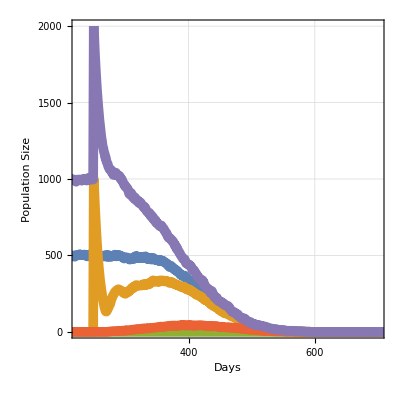
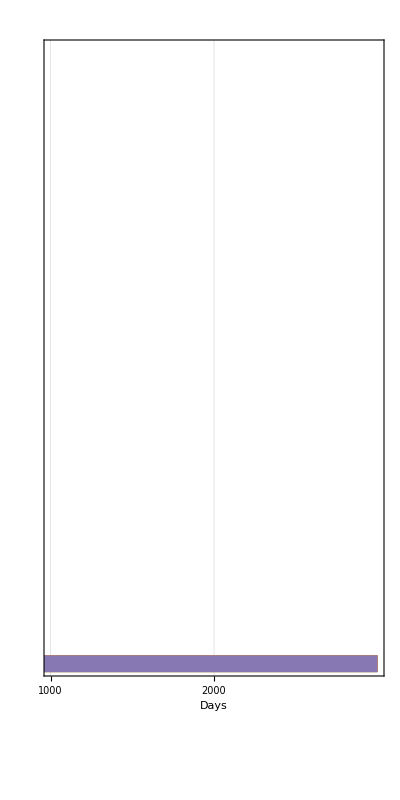
-Graphics- | -Graphics- |          |

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/Fertile_WDXX_1_MedflyClipped_5.pdf

```mathematica
total=Total[(midQuartile//Transpose)[[#]]]&/@idOfInterest;
aspectRatio=2;
popsA=ListLinePlot[total,
Frame->True,
BaseStyle->25,
PlotRange->{{225,700},{0,2000}},
GridLines->Automatic,
FrameStyle->{
{Directive[Gray,Thickness[.0075]],Directive[Gray,Dashed,Thickness[.0025]]},
{Directive[Gray,Thickness[.0075]],Directive[Gray,Thickness[.0075]]}
},
ImageSize->{Automatic,500},
AspectRatio->1,
FrameTicks->{{Range[0,2000,500],None},{Range[0,900,100],None}},
PlotStyle->Thickness[.0175],
FrameLabel->(Style[#,Gray,45]&/@{"Days","Population Size"})
];
popsB=ListLinePlot[total,
Frame->True,
BaseStyle->25,
PlotRange->{{1000,3000},{0,2000}},
GridLines->Automatic,
FrameStyle->{
{Directive[Gray,Dashed,Thickness[.005]],Directive[Gray,Thickness[.015]]},
{Directive[Gray,Thickness[.015]],Directive[Gray,Thickness[.015]]}
},
ImageSize->{Automatic,500},
AspectRatio->aspectRatio,
FrameTicks->{{None,Range[0,2000,500]},{Range[1000,2000,1000],None}},
PlotStyle->Thickness[.03],
FrameLabel->(Style[#,White,45]&/@{"Days",""})
];
labels={"Female","D","R","B","Total"};
legend=SwatchLegend[ColorData[97,"ColorList"][[1;;Length[labels]]],labels,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,20],
LegendLabel->Style["",30]
];
Grid[{{popsA,popsB,"        ",legend}},Spacings->{0,0}]
Export[Directory[]<>"/images/"<>StringSplit[folder,"/"][[3]]<>"_"<>ToString[folderID]<>"_MedflyClipped_"<>ToString[experimentID//Round]<>".pdf",%,ImageSize->2000]
```

## Sweep

N = 1000

```mathematica
ρValues={
.00001*10^-3,.00003*10^-3,.00005*10^-3,.00007*10^-3,.00009*10^-3,
.0001*10^-3,.0003*10^-3,.0005*10^-3,.0007*10^-3,.0009*10^-3,
.001*10^-3,.003*10^-3,.005*10^-3,.007*10^-3,.009*10^-3,
.01*10^-3,.03*10^-3,.05*10^-3,.07*10^-3,.09*10^-3,
.1*10^-3,.3*10^-3,.5*10^-3,.7*10^-3,.9*10^-3,
1*10^-3,3*10^-3,5*10^-3,7*10^-3,9*10^-3,
10*10^-3,30*10^-3,50*10^-3,70*10^-3,90*10^-3,
100*10^-3,300*10^-3,500*10^-3,700*10^-3,900*10^-3
}//N;
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
folder="./Datasets/Fertile_WDXX/N001/";
fileNames=FileNames[folder<>"AF1_Aggregate*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[(Import[#][[All,2;;All]])&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
fileNames//Length
Length/@{ρValues,experimentsIDs}
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40}}

1600

{40,40}

{0.975,0.95,0.975,0.975,0.95,0.95,1.,0.95,0.975,0.975,1.,0.95,1.,0.975,1.,0.95,0.95,0.925,0.925,0.9,0.875,0.725,0.6,0.575,0.35,0.575,0.125,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.0000117798,0.0000601201,0.000123491,0.000812427}

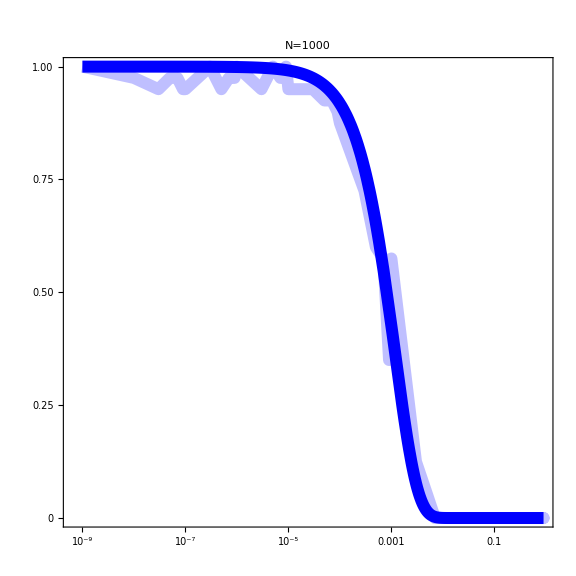
-Graphics- | 0.99 | 0.0000117798
0.95 | 0.0000601201
0.9 | 0.000123491
0.5 | 0.000812427

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/ResponseCurveN001.pdf

```mathematica
Clear[nlm,fitPlot1,x,k,a,c]
probabilities=Table[
experimentPositions=Position[fileNamesIDs,{1,index,_}]//Flatten;
(*Get final values*)
lastValues=Last/@dataCorrected[[experimentPositions]];
(*Calculate crash probability*)
finalPopulation=Total/@lastValues;
Count[finalPopulation,0]/Length[finalPopulation]
,{index,1,experimentsIDs//Length}]//N
coordinates={ρValues,probabilities}//Transpose//Prepend[#,{0.000000001,1}]&//Append[#,{.1,0}]&;
dataPlot=ListLogLinearPlot[
coordinates,
BaseStyle->30,
Joined->True,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameTicks->{
{{{0,"0"},{.25,"0.25"},{.5,"0.50"},{.75,"0.75"},{1,"1.00"}},None},
{{{10^-9,"10^-9"},{10^-7,"10^-7"},{10^-5,"10^-5"},{10^-3,"10^-3"},{10^-1,"10^-1"}},None}
},
FrameTicksStyle->35,
FrameStyle->Directive[Gray,Thickness[.005]],
FrameLabel->{{None,Rotate["P_(elimination)",-180Degree]},{None,"ρ"}},
PlotRange->All,
PlotStyle->{Opacity[.25],Blue,Thickness[.015]},
GridLines->Automatic,
PlotLabel->"N=1000"
];
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
nlm=NonlinearModelFit[coordinates,prototypeFunction[x,k,c],{k,c},x];
probs={.99,.95,.9,.5};
props=Quiet[Solve[nlm[x]==#,x][[1,1,2]]]&/@probs
fitPlot1=LogLinearPlot[
nlm[x],{x,.000000001,.9},
PlotStyle->{Thickness[.015],Blue}
];
a=Show[dataPlot,fitPlot1,ImageSize->Large];
Grid[{{a,Grid[Transpose[{probs,props}]]}}]
Export[Directory[]<>"/images/ResponseCurveN001.pdf",%,ImageSize->2000]
```

```mathematica
sur
```

N = 10000

```mathematica
ρValues={
.00001*10^-3,.00003*10^-3,.00005*10^-3,.00007*10^-3,.00009*10^-3,
.0001*10^-3,.0003*10^-3,.0005*10^-3,.0007*10^-3,.0009*10^-3,
.001*10^-3,.003*10^-3,.005*10^-3,.007*10^-3,.009*10^-3,
.01*10^-3,.03*10^-3,.05*10^-3,.07*10^-3,.09*10^-3,
.1*10^-3,.3*10^-3,.5*10^-3,.7*10^-3,.9*10^-3,
1*10^-3,3*10^-3,5*10^-3,7*10^-3,9*10^-3,
10*10^-3,30*10^-3,50*10^-3,70*10^-3,90*10^-3,
100*10^-3,300*10^-3,500*10^-3,700*10^-3,900*10^-3
}//N;
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
folder="./Datasets/Fertile_WDXX/N010/";
fileNames=FileNames[folder<>"AF1_Aggregate*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[(Import[#][[All,2;;All]])&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
fileNames//Length
Length/@{ρValues,experimentsIDs}
```

{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{2,28},{2,29},{2,30},{2,31},{2,32},{2,33},{2,34},{2,35},{2,36},{2,37},{2,38},{2,39},{2,40}}

1599

{40,40}

{0.95,0.975,1.,0.95,0.925,0.975,1.,1.,0.9,0.95,0.9,0.95,0.95,0.85,0.95,0.875,0.85,0.575,0.675,0.425,0.5,0.075,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.26194×10^-6,6.4405×10^-6,0.0000132293,0.0000870331}

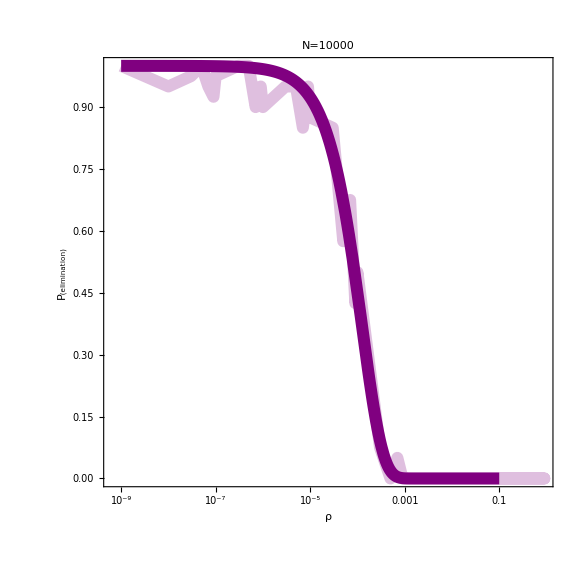
-Graphics- | 0.99 | 1.26194×10^-6
0.95 | 6.4405×10^-6
0.9 | 0.0000132293
0.5 | 0.0000870331

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/ResponseCurveN010.pdf

```mathematica
Clear[nlm,fitPlot2,x,k,c]
probabilities=Table[
experimentPositions=Position[fileNamesIDs,{2,index,_}]//Flatten;
(*Get final values*)
lastValues=Last/@dataCorrected[[experimentPositions]];
(*Calculate crash probability*)
finalPopulation=Total/@lastValues;
Count[finalPopulation,0]/Length[finalPopulation]
,{index,1,experimentsIDs//Length}]//N
coordinates={ρValues,probabilities}//Transpose//Prepend[#,{0.000000001,1}]&//Append[#,{.1,0}]&;
dataPlot=ListLogLinearPlot[
coordinates,
BaseStyle->30,
Joined->True,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameTicksStyle->25,
FrameStyle->Directive[Gray,Thickness[.005]],
FrameLabel->{"ρ","P_(elimination)"},
PlotRange->All,
PlotStyle->{Opacity[.25],Purple,Thickness[.015]},
GridLines->Automatic,
PlotLabel->"N=10000"
];
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
nlm=NonlinearModelFit[coordinates,prototypeFunction[x,k,c],{k,c},x];
probs={.99,.95,.9,.5};
props=Quiet[Solve[nlm[x]==#,x][[1,1,2]]]&/@probs
fitPlot1=LogLinearPlot[
nlm[x],{x,.000000001,.1},
PlotStyle->{Thickness[.015],Purple}
];
b=Show[dataPlot,fitPlot1,ImageSize->Large];
Grid[{{b,Grid[Transpose[{probs,props}]]}}]
Export[Directory[]<>"/images/ResponseCurveN010.pdf",%,ImageSize->2000]
```

N = 100000

```mathematica
ρValues={
.00001*10^-3,.00003*10^-3,.00005*10^-3,.00007*10^-3,.00009*10^-3,
.0001*10^-3,.0003*10^-3,.0005*10^-3,.0007*10^-3,.0009*10^-3,
.001*10^-3,.003*10^-3,.005*10^-3,.007*10^-3,.009*10^-3,
.01*10^-3,.03*10^-3,.05*10^-3,.07*10^-3,.09*10^-3,
.1*10^-3,.3*10^-3,.5*10^-3,.7*10^-3,.9*10^-3,
1*10^-3,3*10^-3,5*10^-3,7*10^-3,9*10^-3,
10*10^-3,30*10^-3,50*10^-3,70*10^-3,90*10^-3,
100*10^-3,300*10^-3,500*10^-3,700*10^-3,900*10^-3
}//N;
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
folder="./Datasets/Fertile_WDXX/N100/";
fileNames=FileNames[folder<>"AF1_Aggregate*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[(Import[#][[All,2;;All]])&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
fileNames//Length
Length/@{ρValues,experimentsIDs}
```

{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{3,26},{3,27},{3,28},{3,29},{3,30},{3,31},{3,32},{3,33},{3,34},{3,35},{3,36},{3,37},{3,38},{3,39},{3,40}}

1600

{40,40}

{0.95,1.,0.975,0.975,0.95,0.975,0.975,0.9,0.875,0.825,0.9,0.7,0.625,0.625,0.475,0.475,0.1,0.025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.20922×10^-7,6.17142×10^-7,1.26766×10^-6,8.33969×10^-6}

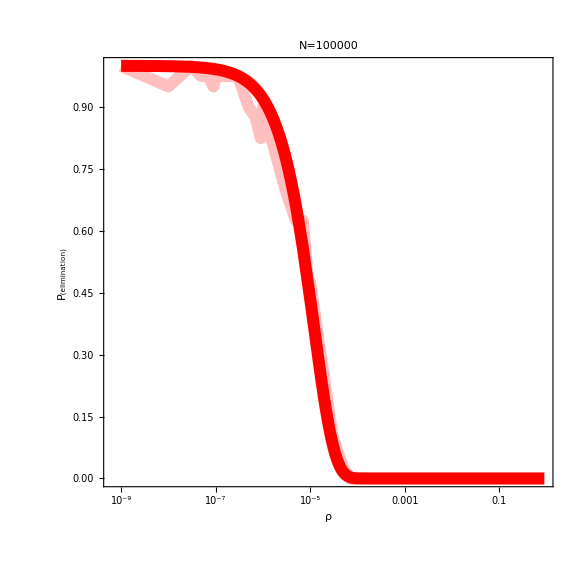
-Graphics- | 0.99 | 1.20922×10^-7
0.95 | 6.17142×10^-7
0.9 | 1.26766×10^-6
0.5 | 8.33969×10^-6

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/ResponseCurveN100.pdf

```mathematica
Clear[nlm,fitPlot2,x,k,c]
probabilities=Table[
experimentPositions=Position[fileNamesIDs,{3,index,_}]//Flatten;
(*Get final values*)
lastValues=Last/@dataCorrected[[experimentPositions]];
(*Calculate crash probability*)
finalPopulation=Total/@lastValues;
Count[finalPopulation,0]/Length[finalPopulation]
,{index,1,experimentsIDs//Length}]//N
coordinates={ρValues,probabilities}//Transpose//Prepend[#,{0.000000001,1}]&//Append[#,{.1,0}]&;
dataPlot=ListLogLinearPlot[
coordinates//Sort,
BaseStyle->30,
Joined->True,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameTicksStyle->25,
FrameStyle->Directive[Gray,Thickness[.005]],
FrameLabel->{"ρ","P_(elimination)"},
PlotRange->All,
PlotStyle->{Opacity[.25],Red,Thickness[.015]},
GridLines->Automatic,
PlotLabel->"N=100000"
];
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
nlm=NonlinearModelFit[coordinates,prototypeFunction[x,k,c],{k,c},x];
probs={.99,.95,.9,.5};
props=Quiet[Solve[nlm[x]==#,x][[1,1,2]]]&/@probs
fitPlot1=LogLinearPlot[
nlm[x],{x,.000000001,.9},
PlotStyle->{Thickness[.015],Red}
];
d=Show[dataPlot,fitPlot1,ImageSize->Large];
Grid[{{d,Grid[Transpose[{probs,props}]]}}]
Export[Directory[]<>"/images/ResponseCurveN100.pdf",%,ImageSize->2000]
```

All

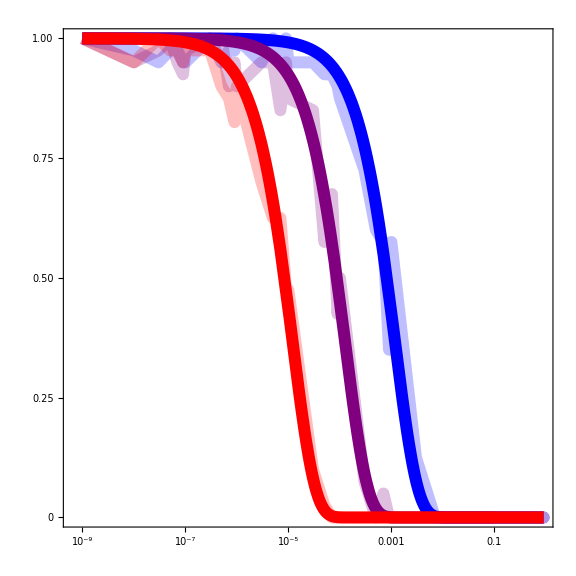

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/images/ResponseCurveOverlay.pdf

```mathematica
Grid[{
{
Show[a,b,d,
FrameTicksStyle->30,
BaseStyle->40,
PlotLabel->None,
AspectRatio->1
]},
{},
{
SwatchLegend[{Blue,Purple,Red},{"1000","10000","100000"},
LegendMarkerSize->20,
LabelStyle->Directive[Gray,20],
LegendLabel->Placed[Style["Population Size: ",30],Left],
LegendLayout->"Row"
]
}
}]
Export[Directory[]<>"/images/ResponseCurveOverlay.pdf",%]
```

## Model Fits

First Plot

```mathematica
dataRaw=Import["./ModelFits/modelFit.csv"];
labels=dataRaw[[1,3;;All]];
data=dataRaw[[2;;All,3;;All]];
(**)
plotOneIndices=Flatten[Position[labels,#]&/@{"A_M_Pred","A_Av_M_Obs","B_M_Pred","B_Av_M_Obs","C_M_Pred","C_Av_M_Obs","D_M_Pred","D_Av_M_Obs"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Generation","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Males",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"A_F_Pred","A_Av_F_Obs","B_F_Pred","B_Av_F_Obs","C_F_Pred","C_Av_F_Obs","D_F_Pred","D_Av_F_Obs"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Females",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;4]],{"1","2","3","4"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["./images/Drosophila_ModelFits.pdf",grid]
```

Second Plot

```mathematica
dataRaw=Import["ModelFits/modelFit2.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]];
(**)
plotOneIndices=Flatten[Position[labels,#]&/@{"D_Female_Pred","D_D_Allele_Pred","D_W_Allele_Pred","D_R_Allele_Pred","D_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Days","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Fitted",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"I_Female_Pred","I_D_Allele_Pred","I_W_Allele_Pred","I_R_Allele_Pred","I_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Ideal",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;5]],{"B","D","XX","R","W"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["./images/Drosophila_PopDynamics.pdf",grid]
```

Third Plot

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9

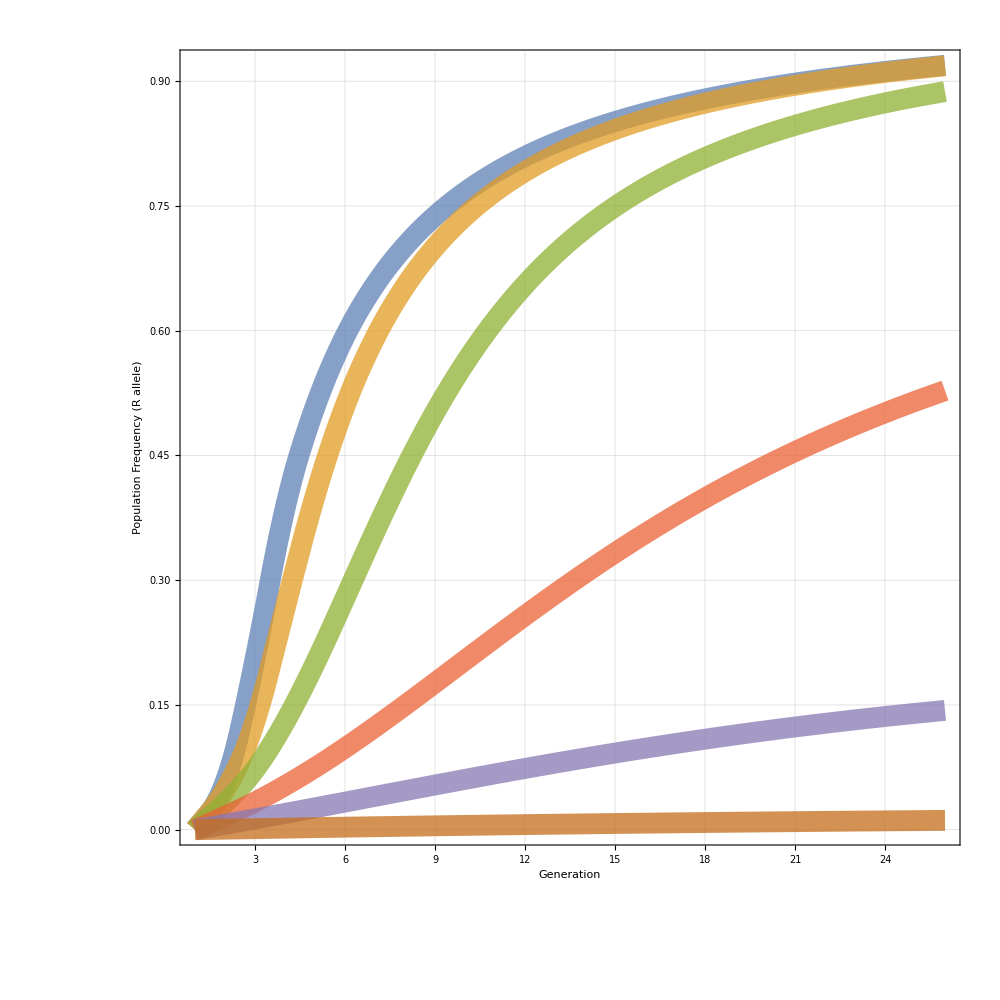
-Graphics- |

./images/Drosophila_DriveAlleleFrequencyAtRelease01.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
rawData=Import["ModelFits/DmPlot01.csv"][[2;;All]];
dataTitle=rawData[[1,2;;All]];
data=rawData[[2;;All,2;;All]]//Transpose;
(**)
plot=ListLinePlot[data,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[dataTitle]]])),
AspectRatio->1,
InterpolationOrder->2,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->40,
FrameLabel->(Style[#,Gray,60]&/@{"Generation","Population Frequency (R allele)"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;6]],dataTitle,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["",30]
];
Grid[{{plot,swatch}}]
Export["./images/Drosophila_DriveAlleleFrequencyAtRelease01.pdf",%]
```

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9

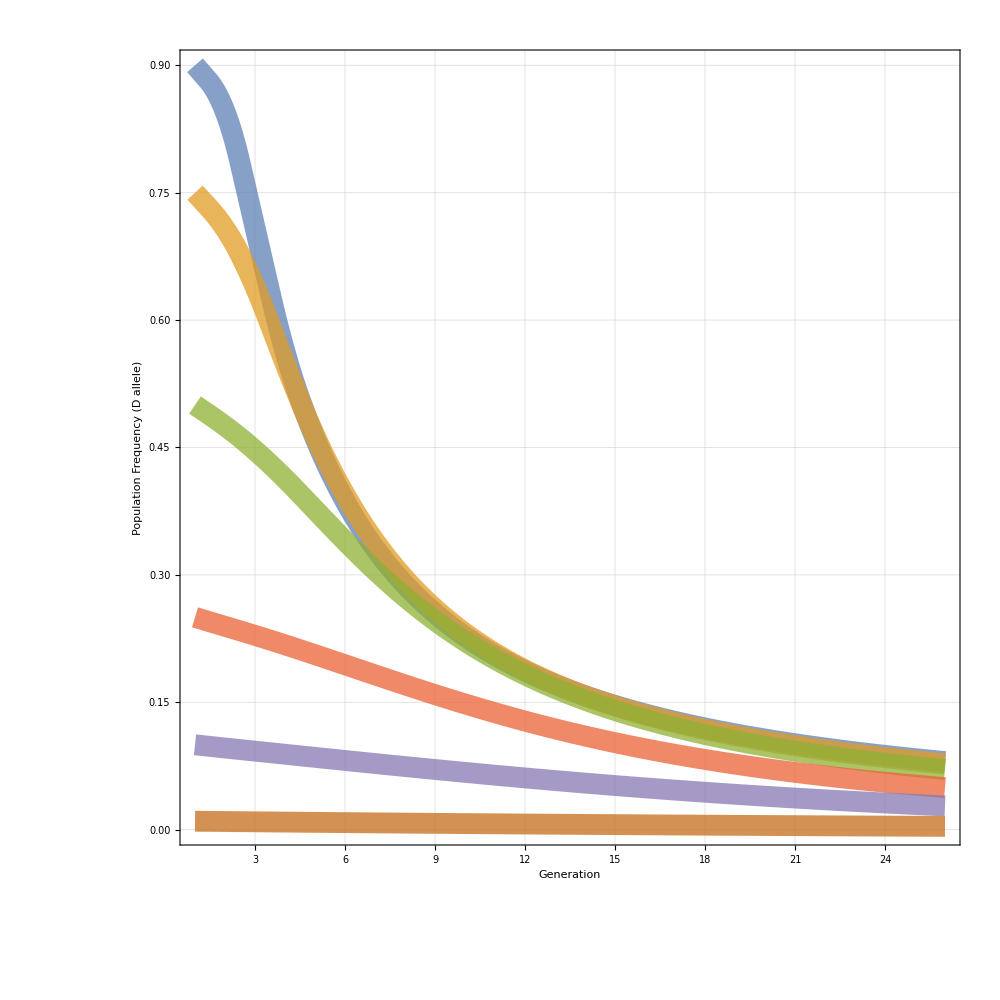
-Graphics- |

./images/Drosophila_DriveAlleleFrequencyAtRelease02.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
rawData=Import["ModelFits/DmPlot02.csv"][[2;;All]];
dataTitle=rawData[[1,2;;All]];
data=rawData[[2;;All,2;;All]]//Transpose;
(**)
plot=ListLinePlot[data,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[dataTitle]]])),
AspectRatio->1,
InterpolationOrder->2,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->40,
FrameLabel->(Style[#,Gray,60]&/@{"Generation","Population Frequency (D allele)"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;6]],dataTitle,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["",30]
];
Grid[{{plot,swatch}}]
Export["./images/Drosophila_DriveAlleleFrequencyAtRelease02.pdf",%]
```